{{739.84,42.1025},{686.44,39.8878},{635.04,37.8435},{585.64,35.8347},{538.24,33.9261},{492.84,32.1093},{449.44,30.34},{408.04,28.675},{368.64,27.0896},{331.24,25.5858},{295.84,24.1258},{262.44,22.763},{231.04,21.4922},{201.64,20.3235},{174.24,19.182},{148.84,18.2014},{125.44,17.2128},{104.04,16.4086},{84.64,15.5203},{67.24,14.8272},{51.84,14.1649},{38.44,13.6483},{27.04,13.0886},{17.64,12.7383},{1.44,11.2084}}

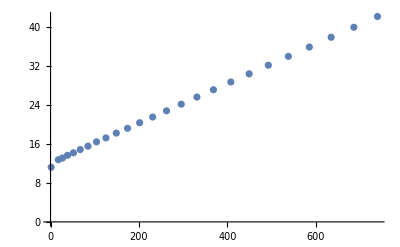

```mathematica
h={27.2,26.2,25.2,24.2,23.2,22.2,21.2,20.2,19.2,18.2,17.2,16.2,15.2,14.2,13.2,12.2,11.2,10.2,9.2,8.2,7.2,6.2,5.2,4.2,1.2};
t={1.24414,1.23387,1.22545,1.21687,1.20927,1.20265,1.19630,1.19145,1.18782,1.18567,1.18434,1.18538,1.18910,1.19634,1.20548,1.22144,1.23970,1.26834,1.29884,1.34469,1.40262,1.48369,1.58652,1.74153,3.05620};

data=Table[{h[[i]]^2,t[[i]]^2h[[i]]},{i,1,25}]
pd=ListPlot[data]
```

```mathematica
data2=Table[data[[i]],{i,1,22}]
fd=Fit[data2,{1,x},x]
```

{{739.84,42.1025},{686.44,39.8878},{635.04,37.8435},{585.64,35.8347},{538.24,33.9261},{492.84,32.1093},{449.44,30.34},{408.04,28.675},{368.64,27.0896},{331.24,25.5858},{295.84,24.1258},{262.44,22.763},{231.04,21.4922},{201.64,20.3235},{174.24,19.182},{148.84,18.2014},{125.44,17.2128},{104.04,16.4086},{84.64,15.5203},{67.24,14.8272},{51.84,14.1649},{38.44,13.6483}}

```mathematica
12.129730054657612+0.04050802981610131 x
```

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RegressionReport::shdw: Symbol "RegressionReport" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

RSquared::shdw: Symbol "RSquared" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

Regress::shdw: Symbol "Regress" appears in multiple contexts {"LinearRegression`", "Global`"}; definitions in context "LinearRegression`" may shadow or be shadowed by other definitions.

```mathematica
Regress[data2,{1,x},x,RegressionReport->{RSquared}]
```

```mathematica
{RSquared->0.9999878978767576}
```

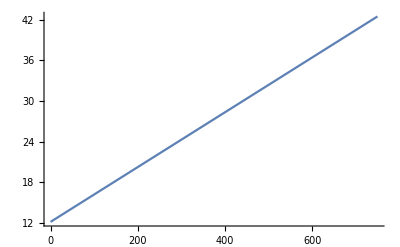

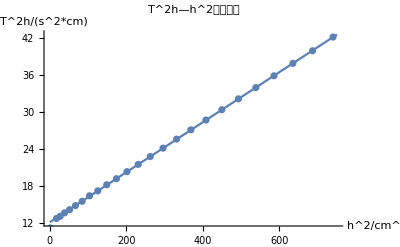

```mathematica
Plot[fd,{x,0,750}]
Show[%,pd,PlotLabel->"T^2h—h^2变化曲线",AxesLabel->{"h^2/cm^2","T^2h/(s^2*cm)"}]
```

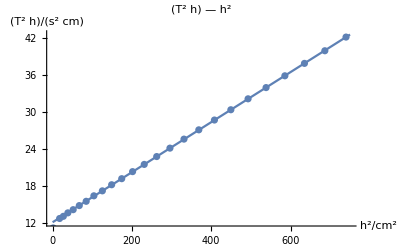

```mathematica
Show[%32,AxesLabel->{HoldForm[h^2/cm^2],HoldForm[(T^2 h)/(s^2 cm)]},PlotLabel->HoldForm[(T^2 h) — h^2],LabelStyle->{GrayLevel[0]}]
```

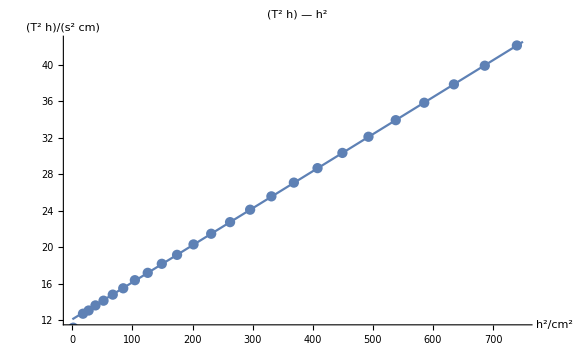

```mathematica
Show[%33,ImageSize->Large]
```

```mathematica
Show[%80,ImageSize->Large]
```

Show::gtype: Out is not a type of graphics.

Show[%80,ImageSize→Large]

{{27.2,1.24414},{26.2,1.23387},{25.2,1.22545},{24.2,1.21687},{23.2,1.20927},{22.2,1.20265},{21.2,1.1963},{20.2,1.19145},{19.2,1.18782},{18.2,1.18567},{17.2,1.18434},{16.2,1.18538},{15.2,1.1891},{14.2,1.19634},{13.2,1.20548},{12.2,1.22144},{11.2,1.2397},{10.2,1.26834},{9.2,1.29884},{8.2,1.34469},{7.2,1.40262},{6.2,1.48369},{5.2,1.58652},{4.2,1.74153},{1.2,3.0562},{-4.1,1.74241},{-6.2,1.48457},{-7.3,1.40318},{-9.3,1.2978},{-10.3,1.26552},{-11.3,1.24054},{-12.3,1.22057},{-13.3,1.20625},{-14.3,1.19603},{-15.3,1.18931},{-16.3,1.18544},{-17.3,1.18452},{-18.3,1.18469},{-19.3,1.18729},{-20.3,1.19061},{-21.3,1.19605},{-22.3,1.20192},{-23.3,1.20906},{-24.3,1.21644},{-25.3,1.22572},{-26.3,1.2332}}

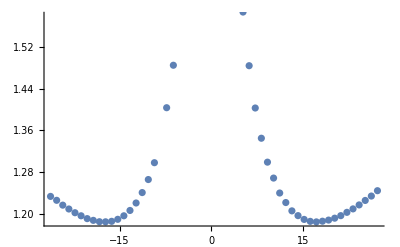

```mathematica
H={27.2,26.2,25.2,24.2,23.2,22.2,21.2,20.2,19.2,18.2,17.2,16.2,15.2,14.2,13.2,12.2,11.2,10.2,9.2,8.2,7.2,6.2,5.2,4.2,1.2,-4.1,-6.2,-7.3,-9.3,-10.3,-11.3,-12.3,-13.3,-14.3,-15.3,-16.3,-17.3,-18.3,-19.3,-20.3,-21.3,-22.3,-23.3,-24.3,-25.3,-26.3};
T={1.24414,1.23387,1.22545,1.21687,1.20927,1.20265,1.19630,1.19145,1.18782,1.18567,1.18434,1.18538,1.18910,1.19634,1.20548,1.22144,1.23970,1.26834,1.29884,1.34469,1.40262,1.48369,1.58652,1.74153,3.05620,1.74241,1.48457,1.40318,1.29780,1.26552,1.24054,1.22057,1.20625,1.19603,1.18931,1.18544,1.18452,1.18469,1.18729,1.19061,1.19605,1.20192,1.20906,1.21644,1.22572,1.23320};
Data3=Table[{H[[i]],T[[i]]},{i,1,46}]
pp=ListPlot[Data3]
```

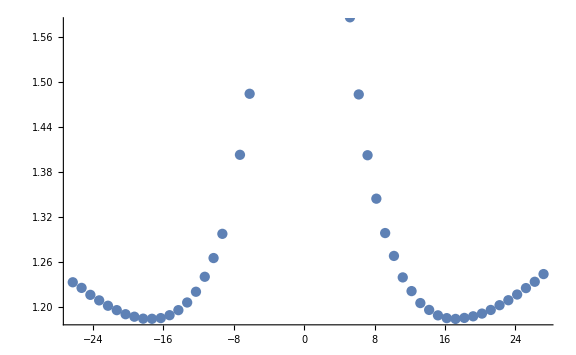

```mathematica
Show[pp,ImageSize->Large]
```

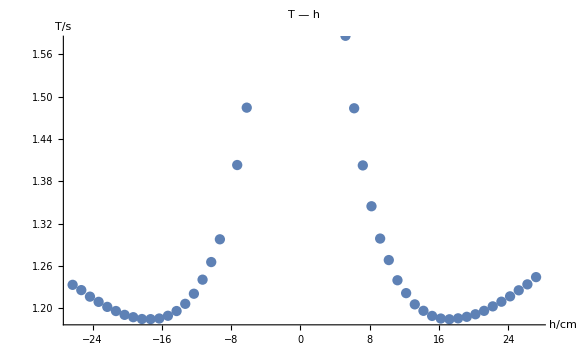

```mathematica
Show[%37,AxesLabel->{HoldForm[h/cm],HoldForm[T/s]},PlotLabel->HoldForm[T — h],LabelStyle->{GrayLevel[0]}]
```

```mathematica
ff=Interpolation[Data3]
```

InterpolatingFunction[{{-26.3, 27.2}}, <>]

```mathematica
l1=Plot[1.20,{x,-25,25},PlotStyle->Dashed];
l2=Plot[1.19,{x,-25,25},PlotStyle->Dashed];
l3=Plot[1.21,{x,-25,25},PlotStyle->Dashed];
```

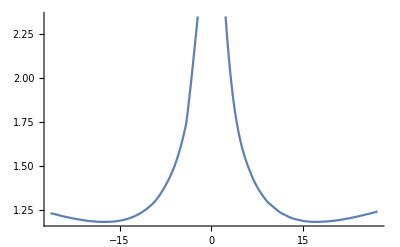

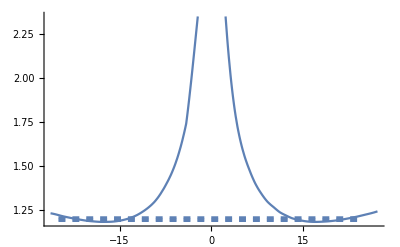

```mathematica
Plot[ff[x],{x,-26.3,27.2}]
Show[%,l1,l2,l3]
```

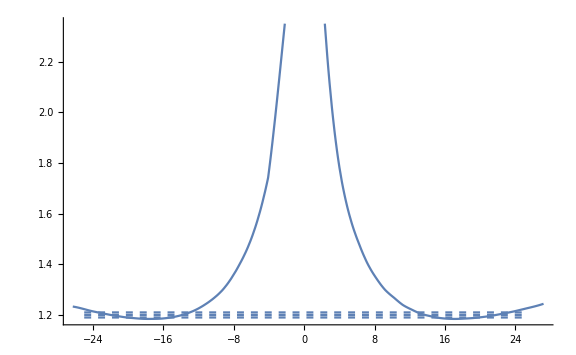

```mathematica
Show[%159,ImageSize->Large]
```

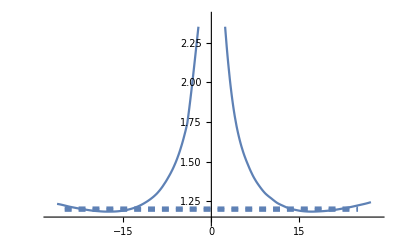

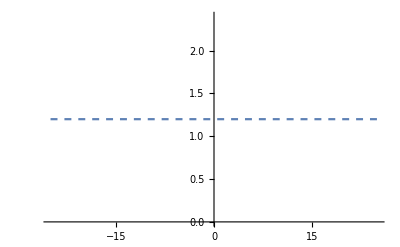

Plot::nonopt: Options expected (instead of {x, -25, 25}) beyond position 2 in Plot[1.19, PlotStyle → Dashed, {x, -25, 25}]. An option must be a rule or a list of rules.

Plot[1.19,PlotStyle→Dashed,{x,-25,25}]

Plot::nonopt: Options expected (instead of {x, -25, 25}) beyond position 2 in Plot[1.21, PlotStyle → Dashed, {x, -25, 25}]. An option must be a rule or a list of rules.

Plot[1.21,PlotStyle→Dashed,{x,-25,25}]

```mathematica
Show[%160,ImageSize->Full]
```

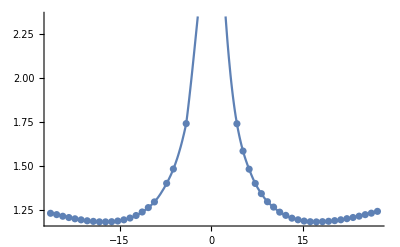

```mathematica
Show[%,pp]
```

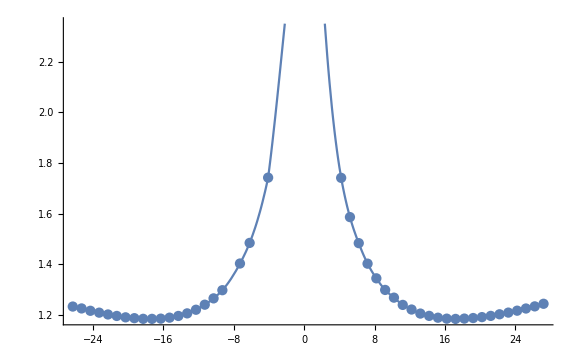

```mathematica
Show[%43,ImageSize->Large]
```

```mathematica
ff[-20.15]
```

1.19001